```mathematica
Sum[ n/(a b)-b,{a,2,Floor[n^(1/3)]},{b,a+1,Floor[(n/a)^1/2]}]
```

$Aborted

```mathematica
FF[n_] := Sum[ Floor[n/(a b)]-b,{a,2,Floor[n^(1/3)]},{b,a+1,Floor[(n/a)^(1/2)]}]
```

```mathematica
FF[80]
```

21

```mathematica
-213
```

-213

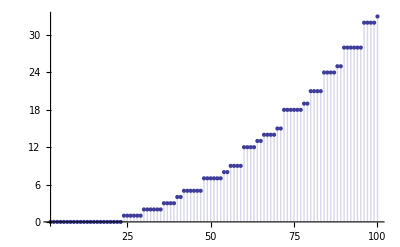

```mathematica
DiscretePlot[ FF[n],{n,2,100}]
```

```mathematica
GG[n_] := Sum[ Floor[n/m]-m,{m,2,Floor[n^(1/2)]}]
```

```mathematica
GG[103]
```

140

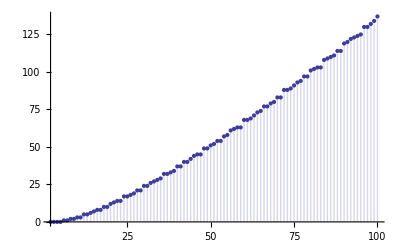

```mathematica
DiscretePlot[GG[n],{n,2,100}]
```

```mathematica
FF[n]
```

∑_(a=2)^Floor[n^(1/3)] ∑_(b=1+a)^Floor[√(n/a)] (-b+Floor[n/(a b)])

```mathematica
∑_(a=2)^Floor[n^(1/3)] ∑_(b=1+a)^Floor[√(n/a)] (-b)+∑_(a=2)^Floor[n^(1/3)] ∑_(b=1+a)^Floor[√(n/a)] (Floor[n/(a b)])
```

$Aborted

```mathematica
∑_(a=2)^Floor[n^(1/3)] ∑_(b=1+a)^Floor[√(n/a)] (-b)
```

$Aborted

```mathematica
∑_(b=1+a)^Floor[√(n/a)] (-b)
```

```mathematica
Expand[1/2 (a-Floor[√(n/a)]) (1+a+Floor[√(n/a)])]
```

a/2+a^2/2-1/2 Floor[√(n/a)]-1/2 Floor[√(n/a)]^2

```mathematica
∑_(a=2)^Floor[n^(1/3)] a/2+∑_(a=2)^Floor[n^(1/3)] a^2/2-∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]-∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]^2
```

1/4 (-2+Floor[n^(1/3)]+Floor[n^(1/3)]^2)+1/12 (-6+Floor[n^(1/3)]+3 Floor[n^(1/3)]^2+2 Floor[n^(1/3)]^3)-∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]-∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]^2

```mathematica
FullSimplify[ 1/4 (-2+Floor[n^(1/3)]+Floor[n^(1/3)]^2)+1/12 (-6+Floor[n^(1/3)]+3 Floor[n^(1/3)]^2+2 Floor[n^(1/3)]^3)-∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]-∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]^2 ]
```

```mathematica
Expand[1/6 (Floor[n^(1/3)] (1+Floor[n^(1/3)]) (2+Floor[n^(1/3)])-6 (1+∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]+∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]^2))]
```

-1+1/3 Floor[n^(1/3)]+1/2 Floor[n^(1/3)]^2+1/6 Floor[n^(1/3)]^3-∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]-∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]^2

```mathematica
F1[n_] :=∑_(a=2)^Floor[n^(1/3)] ∑_(b=1+a)^Floor[√(n/a)] (-b)
```

```mathematica
F2[n_] := -1+1/3 Floor[n^(1/3)]+1/2 Floor[n^(1/3)]^2+1/6 Floor[n^(1/3)]^3-∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]-∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]^2
```

```mathematica
F1[1000]
```

-750

```mathematica
F2[1000]
```

-750

```mathematica
F3[n_] :=-1+1/3 Floor[n^(1/3)]+1/2 Floor[n^(1/3)]^2+1/6 Floor[n^(1/3)]^3-∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]-∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]^2+ ∑_(a=2)^Floor[n^(1/3)] ∑_(b=1+a)^Floor[√(n/a)] (Floor[n/(a b)])
```

```mathematica
F3[100]
```

33

```mathematica
FF[100]
```

33

```mathematica
DiscretePlot[ FF[n],{n,2,100}]
```

-Graphics-

```mathematica
DiscretePlot[ F3[n],{n,2,100}]
```

-Graphics-

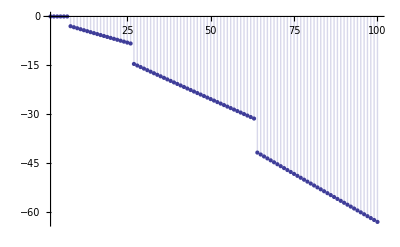

```mathematica
DiscretePlot[-∑_(a=2)^Floor[n^(1/3)] 1/2 √(n/a)-∑_(a=2)^Floor[n^(1/3)] 1/2 (√(n/a))^2,{n,2,100}]
```

```mathematica
FullSimplify[ -1+1/3 Floor[n^(1/3)]+1/2 Floor[n^(1/3)]^2+1/6 Floor[n^(1/3)]^3-∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]-∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]^2+ ∑_(a=2)^Floor[n^(1/3)] ∑_(b=1+a)^Floor[√(n/a)] (Floor[n/(a b)]) ]
```

1/6 (Floor[n^(1/3)] (1+Floor[n^(1/3)]) (2+Floor[n^(1/3)])-6 (1+∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]+∑_(a=2)^Floor[n^(1/3)] 1/2 Floor[√(n/a)]^2-∑_(a=2)^Floor[n^(1/3)] ∑_(b=1+a)^Floor[√(n/a)] Floor[n/(a b)]))